```mathematica
wtApprox=h^2(Derivative[2,0][u][0,0]+Derivative[0,2][u][0,0]);
n=1;
U=Table[u[i h,j k],{i,-n,n},{j,-n,n}];
(Cs=Table[C[Norm[{i,j}]],{i,-n,n},{j,-n,n}])//MatrixForm;
Ds=Table[Norm[{i,j}],{i,-n,n},{j,-n,n}];
cs=Cs//Flatten//Union;
(Cs=Cs/.Table[cs[[i+1]]->C[i],{i,0,Length[cs]-1}])//MatrixForm
cs=Table[C[i],{i,0,Length[cs]-1}];

fn=(Cs U//Flatten//Total)/.k->h;

DToP={Derivative[i_,j_][u][0,0]->x^i y^j,u[0,0]->1};      

taylor=Collect[((fn+O[h]^40//Normal)-wtApprox)/.DToP,h];
```

(C[2] | C[1] | C[2]
C[1] | C[0] | C[1]
C[2] | C[1] | C[2])

```mathematica
conds={};
Do[AppendTo[conds,
CoefficientList[
PolynomialReduce[
Coefficient[taylor,h,i],
x^2+y^2,{x,y}][[2]],
{x,y}]//Flatten//Union],
{i,0,7}];
conds=conds//Flatten//DeleteDuplicates;
(conds=DeleteCases[conds,0])//MatrixForm;
weights=Solve[conds==0&&C[0]==1,cs]//Flatten
```

{C[0]→1,C[1]→-1/5,C[2]→-1/20}

```mathematica
du=(1/h^2(fn/.weights)+O[h]^7)/.DToP;
Assuming[x^2+y^2==0,Simplify[du]]
```

-(y^8 h^6)/10080+O[h]^7

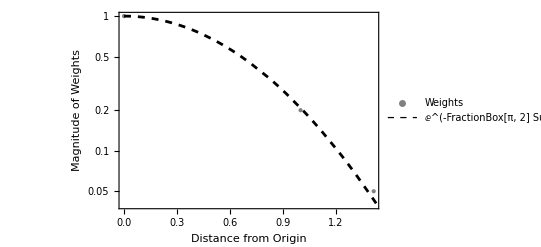

```mathematica
fDs=Flatten[Ds];
fCs=Flatten[Cs]/.weights;
data=Table[{fDs[[i]],Abs[fCs[[i]]]},{i,1,Length[fDs]}]//Union;
p=Show[
ListLogPlot[data,
Frame->True,
FrameLabel->{{"Magnitude of Weights",""},{"Distance from Origin",(2n+1)×(2n+1)"Stencil Size = "}},
LabelStyle->Directive[Medium],
PlotStyle->Directive[Gray,PointSize[Large]],
PlotLegends->{"Weights"}],
LogPlot[ⅇ^(-π/2 r^2),{r,0,20},
PlotLegends->{"ⅇ^(-FractionBox[π, 2] SuperscriptBox[r, 2])"},
PlotStyle->Directive[Black,Dashed,Thickness[.005]]]]
Export["Magnitudes"<>ToString[2n+1]<>".png",p];
```

```mathematica
Log[10,Abs[Cs/.weights]]//MatrixForm//N
Log[10,ⅇ^(-π/2 Ds^2)]//MatrixForm//N
```

(-5.79832 | -3.39008 | -2.74142 | -3.39008 | -5.79832
-3.39008 | -1.36375 | -0.682512 | -1.36375 | -3.39008
-2.74142 | -0.682512 | 0. | -0.682512 | -2.74142
-3.39008 | -1.36375 | -0.682512 | -1.36375 | -3.39008
-5.79832 | -3.39008 | -2.74142 | -3.39008 | -5.79832)

(-5.45751 | -3.41094 | -2.72875 | -3.41094 | -5.45751
-3.41094 | -1.36438 | -0.682188 | -1.36438 | -3.41094
-2.72875 | -0.682188 | 0. | -0.682188 | -2.72875
-3.41094 | -1.36438 | -0.682188 | -1.36438 | -3.41094
-5.45751 | -3.41094 | -2.72875 | -3.41094 | -5.45751)